```mathematica
t=Table[Plot[PDF[GammaDistribution[2,q],x],{x,0,20},Filling->Axis,FrameLabel->{"time","cases"},Frame->True,PlotRangePadding->None,FrameTicks->None,PlotRange->{Automatic,{0,0.2}},Epilog->{White,Line[{{0,0.1},{20,0.1}}],{If[PDF[GammaDistribution[2,q],q]>0.1,Red,Green],Line[{{q,PDF[GammaDistribution[2,q],q]},{q,0.1}}]},Text["hospital capacity",{17,0.105}]},Background->Black,PlotStyle->White,FrameStyle->White,ImageSize->{400,400}],{q,2,7,0.1}];
```

```mathematica
ListAnimate[t]
```

```mathematica
Export["D:\\tmp\\cv.gif",t,DefaultDuration->5,AnimationRepetitions->Infinity]
```

D:\tmp\cv.gif

```mathematica
Assuming
```

```mathematica
expr=Simplify[PDF[GammaDistribution[2,4],x],x>0];
Solve[D[expr,x]==0,x]
```

{{x→4}}

```mathematica
expr
```

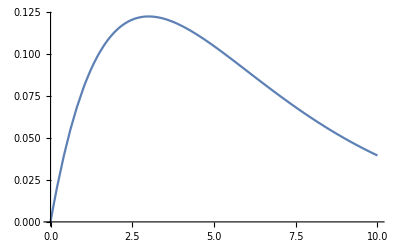

```mathematica
Plot[1/9 ⅇ^(-x/3) x,{x,0,10}]
```

```mathematica
PDF[GammaDistribution[2,3],3]
```

1/(3 ⅇ)